## Test functions for optimization

#### Ackley function

```mathematica
f = -20 Exp[-0.2 √(0.5(x^2+y^2))]-Exp[0.5(Cos[2π x] + Cos[2π y])]+E+20;
Plot3D[f,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

## Results

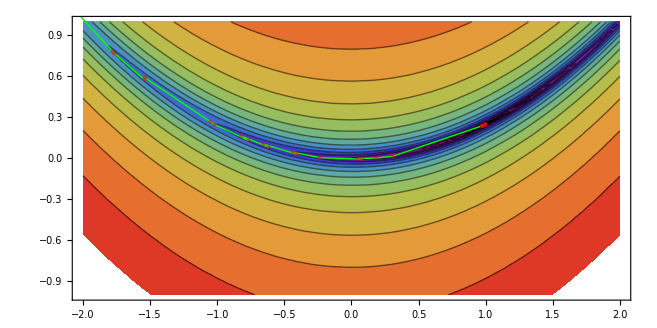

```mathematica
pts = Import["/Users/yangjunjie/work/numerical_optimization/test/dfp_result.csv"];
plt = ContourPlot[(1-x)^2+100*(4y-x^2)^2,{x,-2,2},{y,-1,1},AspectRatio->{1}, Epilog->{Green,Line[pts],Opacity[0.5],PointSize[Medium],Red,Point[pts]},Contours->Table[2^i,{i,-20,20}],ColorFunction->(ColorData["Rainbow"][(Log[2,#]/12)]&),ColorFunctionScaling->False]
```

```mathematica
Export["/Users/yangjunjie/work/numerical_optimization/test/dfp_result.pdf", plt]
```

/Users/yangjunjie/work/numerical_optimization/test/dfp_result.pdf